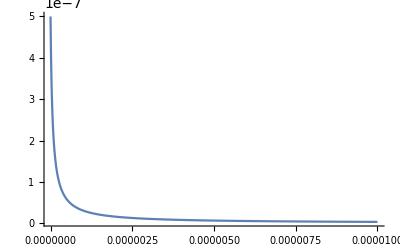

```mathematica
Clear["Global`*"];
Module[{k,A,T,P,FA0,FB0,pA0,pB0,V,v,tMax,R,Ea,sol,pa,y},
R=8.3145;
FA0=0.5*^-6;
FB0=0.5*^-6;
pA0=P*FA0/(FA0+FB0);
pB0=P*FB0/(FA0+FB0);
V=10*^-6;(*10 mL = 1E-5 m^3*)
v=(FA0+FB0)*R*T/P;(*volumetric flow rate - m^3/s*)
P=750000;
k[A_,Ea_,T_]:=A*Exp[-Ea/(R*T)];
sol=FA/.NDSolve[{
FA'[vol]==-k[1,113000,575]*(P*FA[vol]/(FA0+FB0))^1*(P*(FB0-(FA0-FA[vol]))/(FA0+FB0))^1,
FA[0]==FA0
},FA,{vol,0,10*^-6}][[1]][[1]];
Plot[sol[v],{v,0,10*^-6},PlotRange->All]
(*DSolve[{
pA'[t]==-k[A,Ea,T]*pA[t]^m*(pB0-(pA0-pA[t]))^n,
pA[0]==pA0
},pA[t],t]*)

]
```

```mathematica
FA[t_,m_,n_,P_]:=((FA0+FB0)/P)*((0.5*P)^(1-m-n)+(m+n-1)*Exp[-Ea/(R*T)]*A*V/((FA0+FB0)*R*T/P))^(1/(1-m-n))
```

```mathematica
Module[{FA,Ea,R,T,A,FA0,FB0,pA0,pB0,v,VMax,P},
R=8.3145;
Ea=113000;
T=575;
P=750000;
FA0=0.5*^-6;
FB0=0.5*^-6;
pA0=P*FA0/(FA0+FB0);
pB0=P*FB0/(FA0+FB0);
VMax=10;
v=(FA0+FB0)*R*T/P;(*volumetric flow rate - m^3/s*)
FA[A_,V_,m_,n_]:=((FA0+FB0)/P)*((0.5*P)^(1-m-n)+(m+n-1)*Exp[-Ea/(R*T)]*A*V/v)^(1/(1-m-n));
A[m_,n_]:=a/.NSolve[FA[a,VMax,m,n]/FA0==0.5,a,Reals];
Quiet@Table[{m,n,Select[A[m,n],Positive][[1]]},{m,-1,2,0.25},{n,-1,2,0.25}]
]
```

{{{-1.,-1.,1.80476×10^17},{-1.,-0.75,7.74104×10^15},{-1.,-0.5,3.32732×10^14},{-1.,-0.25,1.43328×10^13},{-1.,0.,6.18774×10^11},{-1.,0.25,2.67747×10^10},{-1.,0.5,1.16125×10^9},{-1.,0.75,5.04847×10^7},{-1.,1.,2.20009×10^6},{-1.,1.25,96112.7},{-1.,1.5,4209.14},{-1.,1.75,184.793},{-1.,2.,a}},{{-0.75,-1.,7.74104×10^15},{-0.75,-0.75,3.32732×10^14},{-0.75,-0.5,1.43328×10^13},{-0.75,-0.25,6.18774×10^11},{-0.75,0.,2.67747×10^10},{-0.75,0.25,1.16125×10^9},{-0.75,0.5,5.04847×10^7},{-0.75,0.75,2.20009×10^6},{-0.75,1.,96112.7},{-0.75,1.25,4209.14},{-0.75,1.5,184.793},{-0.75,1.75,a},{-0.75,2.,0.358862}},{{-0.5,-1.,3.32732×10^14},{-0.5,-0.75,1.43328×10^13},{-0.5,-0.5,6.18774×10^11},{-0.5,-0.25,2.67747×10^10},{-0.5,0.,1.16125×10^9},{-0.5,0.25,5.04847×10^7},{-0.5,0.5,2.20009×10^6},{-0.5,0.75,96112.7},{-0.5,1.,4209.14},{-0.5,1.25,184.793},{-0.5,1.5,a},{-0.5,1.75,0.358862},{-0.5,2.,0.0158737}},{{-0.25,-1.,1.43328×10^13},{-0.25,-0.75,6.18774×10^11},{-0.25,-0.5,2.67747×10^10},{-0.25,-0.25,1.16125×10^9},{-0.25,0.,5.04847×10^7},{-0.25,0.25,2.20009×10^6},{-0.25,0.5,96112.7},{-0.25,0.75,4209.14},{-0.25,1.,184.793},{-0.25,1.25,a},{-0.25,1.5,0.358862},{-0.25,1.75,0.0158737},{-0.25,2.,0.000703892}},{{0.,-1.,6.18774×10^11},{0.,-0.75,2.67747×10^10},{0.,-0.5,1.16125×10^9},{0.,-0.25,5.04847×10^7},{0.,0.,2.20009×10^6},{0.,0.25,96112.7},{0.,0.5,4209.14},{0.,0.75,184.793},{0.,1.,a},{0.,1.25,0.358862},{0.,1.5,0.0158737},{0.,1.75,0.000703892},{0.,2.,0.0000312901}},{{0.25,-1.,2.67747×10^10},{0.25,-0.75,1.16125×10^9},{0.25,-0.5,5.04847×10^7},{0.25,-0.25,2.20009×10^6},{0.25,0.,96112.7},{0.25,0.25,4209.14},{0.25,0.5,184.793},{0.25,0.75,a},{0.25,1.,0.358862},{0.25,1.25,0.0158737},{0.25,1.5,0.000703892},{0.25,1.75,0.0000312901},{0.25,2.,1.39434×10^-6}},{{0.5,-1.,1.16125×10^9},{0.5,-0.75,5.04847×10^7},{0.5,-0.5,2.20009×10^6},{0.5,-0.25,96112.7},{0.5,0.,4209.14},{0.5,0.25,184.793},{0.5,0.5,a},{0.5,0.75,0.358862},{0.5,1.,0.0158737},{0.5,1.25,0.000703892},{0.5,1.5,0.0000312901},{0.5,1.75,1.39434×10^-6},{0.5,2.,6.22842×10^-8}},{{0.75,-1.,5.04847×10^7},{0.75,-0.75,2.20009×10^6},{0.75,-0.5,96112.7},{0.75,-0.25,4209.14},{0.75,0.,184.793},{0.75,0.25,a},{0.75,0.5,0.358862},{0.75,0.75,0.0158737},{0.75,1.,0.000703892},{0.75,1.25,0.0000312901},{0.75,1.5,1.39434×10^-6},{0.75,1.75,6.22842×10^-8},{0.75,2.,2.7888×10^-9}},{{1.,-1.,2.20009×10^6},{1.,-0.75,96112.7},{1.,-0.5,4209.14},{1.,-0.25,184.793},{1.,0.,a},{1.,0.25,0.358862},{1.,0.5,0.0158737},{1.,0.75,0.000703892},{1.,1.,0.0000312901},{1.,1.25,1.39434×10^-6},{1.,1.5,6.22842×10^-8},{1.,1.75,2.7888×10^-9},{1.,2.,1.2516×10^-10}},{{1.25,-1.,96112.7},{1.25,-0.75,4209.14},{1.25,-0.5,184.793},{1.25,-0.25,a},{1.25,0.,0.358862},{1.25,0.25,0.0158737},{1.25,0.5,0.000703892},{1.25,0.75,0.0000312901},{1.25,1.,1.39434×10^-6},{1.25,1.25,6.22842×10^-8},{1.25,1.5,2.7888×10^-9},{1.25,1.75,1.2516×10^-10},{1.25,2.,5.62998×10^-12}},{{1.5,-1.,4209.14},{1.5,-0.75,184.793},{1.5,-0.5,a},{1.5,-0.25,0.358862},{1.5,0.,0.0158737},{1.5,0.25,0.000703892},{1.5,0.5,0.0000312901},{1.5,0.75,1.39434×10^-6},{1.5,1.,6.22842×10^-8},{1.5,1.25,2.7888×10^-9},{1.5,1.5,1.2516×10^-10},{1.5,1.75,5.62998×10^-12},{1.5,2.,2.53812×10^-13}},{{1.75,-1.,184.793},{1.75,-0.75,a},{1.75,-0.5,0.358862},{1.75,-0.25,0.0158737},{1.75,0.,0.000703892},{1.75,0.25,0.0000312901},{1.75,0.5,1.39434×10^-6},{1.75,0.75,6.22842×10^-8},{1.75,1.,2.7888×10^-9},{1.75,1.25,1.2516×10^-10},{1.75,1.5,5.62998×10^-12},{1.75,1.75,2.53812×10^-13},{1.75,2.,1.14673×10^-14}},{{2.,-1.,a},{2.,-0.75,0.358862},{2.,-0.5,0.0158737},{2.,-0.25,0.000703892},{2.,0.,0.0000312901},{2.,0.25,1.39434×10^-6},{2.,0.5,6.22842×10^-8},{2.,0.75,2.7888×10^-9},{2.,1.,1.2516×10^-10},{2.,1.25,5.62998×10^-12},{2.,1.5,2.53812×10^-13},{2.,1.75,1.14673×10^-14},{2.,2.,5.19184×10^-16}}}